```mathematica
t[n_,a_]:= (-1)^(Floor[n/a]-Floor[(n-1)/a])
ST[n_,a_] := Sum[ t[j,a],{j,1,n}]
```

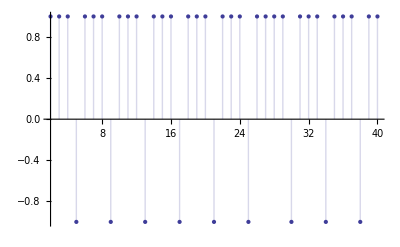

```mathematica
DiscretePlot[ t[n,25/6],{n,2,40}]
```

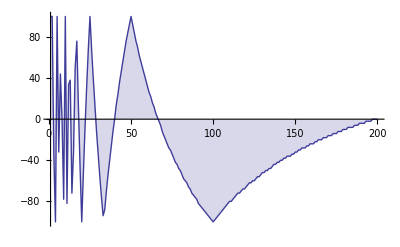

```mathematica
DiscretePlot[ ST[100,n/100],{n,1,200}]
```

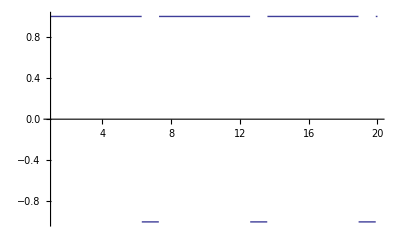

```mathematica
Plot[t[n,6.3],{n,1,20}]
```

```mathematica
pr[n_, va_] := Sum[ 2^k/k,{k,1,Log[va,n]}]
```